```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]
```

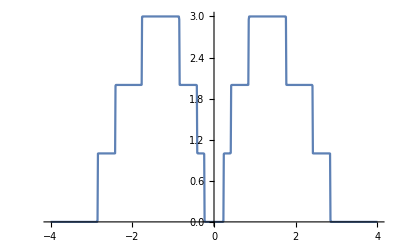

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ],u1=RandomInteger[{1,7}],u2=RandomInteger[{8,14}]},ReplacePart[κ,{{u1,u1},{u2,u2}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ],u1=RandomInteger[{1,4}],u2=RandomInteger[{5,9}],u3=RandomInteger[{10,14}]},ReplacePart[κ,{{u1,u1},{u2,u2},{u3,u3}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_]:=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1],3],Table[imp2[ω,δ,t,ϵ,ϵ1],1]]]
```

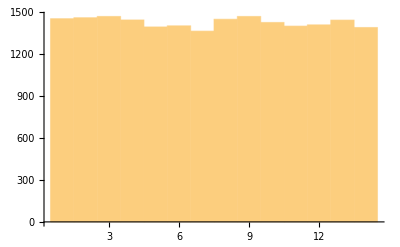

```mathematica
Histogram[Flatten[Table[{Position[set[0,0,0,0,1][[1]],-1][[1,1]],Position[set[0,0,0,0,1][[1]],-1][[2,2]]},10000]]]
```

```mathematica
Flatten[%132]
```

{2,13,3,11,1,9,7,14,1,9,1,8,3,6,4,11,7,8,5,14}

```mathematica
Position[set[0,0,0,0,1][[1]],-1][[1,1]]
```

{{5,5},{9,9}}

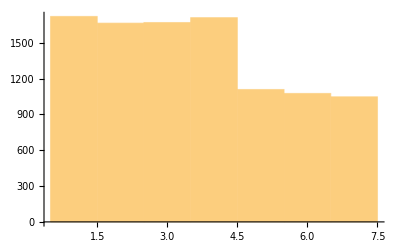

```mathematica
Histogram[Table[Position[set[0,0,0,0,1][[1]],-1][[1,1]],10000]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{a=Inverse[Module[{κ=β[ω,δ,t,ϵ],u1=RandomInteger[{1,7}],u2=RandomInteger[{8,14}]},ReplacePart[κ,{{u1,u1},{u2,u2}}->ω+ⅈ*δ-ϵ1]]],b=Inverse[Module[{κ=β[ω,δ,t,ϵ],u1=RandomInteger[{1,4}],u2=RandomInteger[{5,9}],u3=RandomInteger[{10,14}]},ReplacePart[κ,{{u1,u1},{u2,u2},{u3,u3}}->ω+ⅈ*δ-ϵ1]]]},RandomSample[Join[RandomChoice[{a},3],RandomChoice[{b},1]],4]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],x=T1[1],T=TT[1]},
η=Module[{c=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1],3],Table[imp2[ω,δ,t,ϵ,ϵ1],1]]]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[14]-c[[m]].ConjugateTranspose[x].J.x].c[[m]],{m,1,4}]; J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].T.sl1.T].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];{Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]],Inverse[c[[1]]],Inverse[c[[2]]],Inverse[c[[3]]],Inverse[c[[4]]]}];
η]
```

```mathematica
MatrixForm[Chop[tr1[0,0.0001,1000,0,1][[2]]-ⅈ*0.0001IdentityMatrix[14]]]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.7][[1]],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00440502},{0.01,0.00369302},{0.02,0.0031664},{0.03,0.0025054},{0.04,0.00221618},{0.05,0.00184855},{0.06,0.00158892},{0.07,0.0014129},{0.08,0.00129926},{0.09,0.00124662},{0.1,0.0013128},{0.11,0.00138958},{0.12,0.00149263},{0.13,0.00169502},{0.14,0.00192297},{0.15,0.00234122},{0.16,0.00276633},{0.17,0.00332755},{0.18,0.00428915},{0.19,0.00537094},{0.2,0.00704215},{0.21,0.0093914},{0.22,0.0127609},{0.23,0.0206443},{0.24,0.0271695},{0.25,0.0487566},{0.26,0.0851955},{0.27,0.129427},{0.28,0.176572},{0.29,0.226494},{0.3,0.278238},{0.31,0.334982},{0.32,0.390511},{0.33,0.443482},{0.34,0.492353},{0.35,0.526625},{0.36,0.561228},{0.37,0.59262},{0.38,0.607719},{0.39,0.60863},{0.4,0.603025},{0.41,0.572087},{0.42,0.559633},{0.43,0.602241},{0.44,0.648152},{0.45,0.706178},{0.46,0.761904},{0.47,0.819007},{0.48,0.872242},{0.49,0.929251},{0.5,0.973193},{0.51,1.0383},{0.52,1.07641},{0.53,1.12228},{0.54,1.16864},{0.55,1.20362},{0.56,1.24651},{0.57,1.28138},{0.58,1.3187},{0.59,1.35008},{0.6,1.37607},{0.61,1.39942},{0.62,1.42859},{0.63,1.44583},{0.64,1.46334},{0.65,1.47679},{0.66,1.49377},{0.67,1.51549},{0.68,1.52237},{0.69,1.53234},{0.7,1.53358},{0.71,1.54901},{0.72,1.54712},{0.73,1.54976},{0.74,1.55677},{0.75,1.55097},{0.76,1.55588},{0.77,1.55343},{0.78,1.54855},{0.79,1.54212},{0.8,1.53428},{0.81,1.51329},{0.82,1.49145},{0.83,1.45581},{0.84,1.37471},{0.85,1.19184},{0.86,1.25006},{0.87,1.30485},{0.88,1.35081},{0.89,1.40111},{0.9,1.44608},{0.91,1.50187},{0.92,1.55437},{0.93,1.60095},{0.94,1.65285},{0.95,1.71977},{0.96,1.78427},{0.97,1.83412},{0.98,1.88294},{0.99,1.93944},{1.,1.99384},{1.01,2.02925},{1.02,2.06308},{1.03,2.0581},{1.04,2.01574},{1.05,1.9105},{1.06,1.69877},{1.07,1.40292},{1.08,1.15278},{1.09,1.03262},{1.1,1.02092},{1.11,1.07723},{1.12,1.11883},{1.13,1.14963},{1.14,1.18648},{1.15,1.21121},{1.16,1.20199},{1.17,1.1649},{1.18,1.14127},{1.19,1.13557},{1.2,1.15711},{1.21,1.22709},{1.22,1.26738},{1.23,1.32774},{1.24,1.36962},{1.25,1.43417},{1.26,1.47259},{1.27,1.50576},{1.28,1.54189},{1.29,1.56392},{1.3,1.58997},{1.31,1.61593},{1.32,1.63594},{1.33,1.66167},{1.34,1.68204},{1.35,1.69828},{1.36,1.7331},{1.37,1.73222},{1.38,1.74208},{1.39,1.75433},{1.4,1.76066},{1.41,1.75625},{1.42,1.77029},{1.43,1.77151},{1.44,1.76483},{1.45,1.76605},{1.46,1.77055},{1.47,1.76347},{1.48,1.75531},{1.49,1.7518},{1.5,1.74114},{1.51,1.74234},{1.52,1.73356},{1.53,1.73029},{1.54,1.71783},{1.55,1.70489},{1.56,1.68772},{1.57,1.67229},{1.58,1.67107},{1.59,1.65205},{1.6,1.63384},{1.61,1.60657},{1.62,1.58367},{1.63,1.56262},{1.64,1.52744},{1.65,1.49848},{1.66,1.46665},{1.67,1.40866},{1.68,1.38093},{1.69,1.32153},{1.7,1.26195},{1.71,1.19262},{1.72,1.10093},{1.73,0.991022},{1.74,0.890328},{1.75,0.818157},{1.76,1.01279},{1.77,2.32427},{1.78,2.04863},{1.79,1.90631},{1.8,1.83705},{1.81,1.83198},{1.82,1.67836},{1.83,1.57634},{1.84,1.44076},{1.85,1.3999},{1.86,1.26327},{1.87,1.15807},{1.88,1.14271},{1.89,1.03374},{1.9,0.961737},{1.91,0.941858},{1.92,0.914574},{1.93,0.915851},{1.94,0.961049},{1.95,1.00604},{1.96,1.04015},{1.97,1.09291},{1.98,1.11701},{1.99,1.16143},{2.,1.20646},{2.01,1.2222},{2.02,1.24862},{2.03,1.27717},{2.04,1.29245},{2.05,1.30418},{2.06,1.31739},{2.07,1.32763},{2.08,1.33472},{2.09,1.34146},{2.1,1.35015},{2.11,1.34963},{2.12,1.35361},{2.13,1.35995},{2.14,1.35979},{2.15,1.36421},{2.16,1.36394},{2.17,1.36181},{2.18,1.35682},{2.19,1.34734},{2.2,1.35188},{2.21,1.34016},{2.22,1.33299},{2.23,1.32869},{2.24,1.30873},{2.25,1.30377},{2.26,1.28378},{2.27,1.26802},{2.28,1.26021},{2.29,1.2533},{2.3,1.22981},{2.31,1.20177},{2.32,1.18155},{2.33,1.17338},{2.34,1.14582},{2.35,1.10984},{2.36,1.06454},{2.37,1.01248},{2.38,0.935707},{2.39,0.842103},{2.4,0.703874},{2.41,0.589734},{2.42,1.04769},{2.43,1.00482},{2.44,1.20189},{2.45,1.47695},{2.46,1.67991},{2.47,1.52586},{2.48,1.50436},{2.49,1.22358},{2.5,1.13947},{2.51,1.03083},{2.52,1.0218},{2.53,0.99761},{2.54,0.793991},{2.55,0.873289},{2.56,0.743936},{2.57,0.700265},{2.58,0.625794},{2.59,0.630641},{2.6,0.625854},{2.61,0.642459},{2.62,0.653935},{2.63,0.672362},{2.64,0.69054},{2.65,0.693517},{2.66,0.696014},{2.67,0.692773},{2.68,0.697484},{2.69,0.691939},{2.7,0.684271},{2.71,0.681307},{2.72,0.677613},{2.73,0.667307},{2.74,0.659095},{2.75,0.661395},{2.76,0.659646},{2.77,0.649231},{2.78,0.643916},{2.79,0.639414},{2.8,0.614372},{2.81,0.575145},{2.82,0.516075},{2.83,0.417421},{2.84,0.275724},{2.85,0.976523},{2.86,2.35287},{2.87,4.31426},{2.88,8.22017},{2.89,9.91774},{2.9,12.8859},{2.91,8.94344},{2.92,8.11242},{2.93,6.35572},{2.94,2.23705},{2.95,2.3207},{2.96,1.67022},{2.97,3.53074},{2.98,2.48861},{2.99,3.13182},{3.,1.26572},{3.01,0.440007},{3.02,0.531043},{3.03,1.28156},{3.04,0.782925},{3.05,0.0285905},{3.06,0.0055582},{3.07,0.00382999},{3.08,0.00303519},{3.09,0.00254847},{3.1,0.00205276},{3.11,0.00172389},{3.12,0.00154362},{3.13,0.00138652},{3.14,0.00120694},{3.15,0.00105419},{3.16,0.000941957},{3.17,0.000847511},{3.18,0.000743983},{3.19,0.000695817},{3.2,0.000624552},{3.21,0.000553187},{3.22,0.00052083},{3.23,0.000468629},{3.24,0.000425278},{3.25,0.000381327},{3.26,0.000352559},{3.27,0.000329076},{3.28,0.000303887},{3.29,0.000276172},{3.3,0.000253623},{3.31,0.000233305},{3.32,0.000210159},{3.33,0.000207803},{3.34,0.000187613},{3.35,0.000173091},{3.36,0.000162023},{3.37,0.000149728},{3.38,0.000138659},{3.39,0.00013234},{3.4,0.000125698},{3.41,0.000114396},{3.42,0.000107101},{3.43,0.0000977308},{3.44,0.0000949083},{3.45,0.0000881139},{3.46,0.0000854819},{3.47,0.0000788596},{3.48,0.0000716955},{3.49,0.0000693729},{3.5,0.0000646142},{3.51,0.0000613995},{3.52,0.0000571768},{3.53,0.0000533602},{3.54,0.0000522738},{3.55,0.0000493214},{3.56,0.000045786},{3.57,0.0000434802},{3.58,0.0000393353},{3.59,0.0000396861},{3.6,0.0000361187},{3.61,0.0000360118},{3.62,0.0000337976},{3.63,0.0000323207},{3.64,0.0000295503},{3.65,0.0000289539},{3.66,0.0000274629},{3.67,0.0000259007},{3.68,0.0000248001},{3.69,0.00002394},{3.7,0.0000227633},{3.71,0.0000209459},{3.72,0.000020197},{3.73,0.0000189042},{3.74,0.0000181329},{3.75,0.0000169548},{3.76,0.0000168196},{3.77,0.0000163967},{3.78,0.0000148371},{3.79,0.0000146026},{3.8,0.0000142349},{3.81,0.0000132822},{3.82,0.0000128716},{3.83,0.0000119984},{3.84,0.0000116633},{3.85,0.0000111712},{3.86,0.0000109345},{3.87,0.0000102433},{3.88,9.77205×10^-6},{3.89,9.38975×10^-6},{3.9,8.96361×10^-6},{3.91,8.60647×10^-6},{3.92,8.18371×10^-6},{3.93,8.01068×10^-6},{3.94,7.6003×10^-6},{3.95,7.42326×10^-6},{3.96,7.05426×10^-6},{3.97,6.7217×10^-6},{3.98,6.38369×10^-6},{3.99,6.09919×10^-6},{4.,5.99705×10^-6}}

```mathematica
Export["9imp7.csv",%171]
```

9imp7.csv

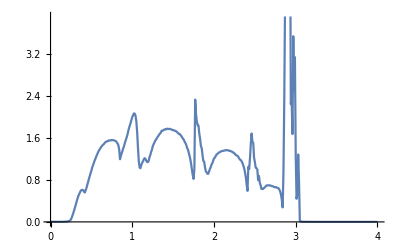

```mathematica
ListPlot[%171,Joined->True]
```

```mathematica
Export["9imp5.csv",%173]
```

9imp5.csv

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5][[1]],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000910823},{0.01,0.000732457},{0.02,0.000573977},{0.03,0.000498217},{0.04,0.00041387},{0.05,0.000352857},{0.06,0.000328948},{0.07,0.000318078},{0.08,0.000355906},{0.09,0.000392288},{0.1,0.000465358},{0.11,0.000579417},{0.12,0.000713593},{0.13,0.00090291},{0.14,0.00113477},{0.15,0.00140892},{0.16,0.00183041},{0.17,0.00236988},{0.18,0.00296695},{0.19,0.00401275},{0.2,0.00521535},{0.21,0.00749617},{0.22,0.0112428},{0.23,0.0185758},{0.24,0.0349193},{0.25,0.107207},{0.26,0.191795},{0.27,0.274697},{0.28,0.353949},{0.29,0.430036},{0.3,0.503247},{0.31,0.565611},{0.32,0.619981},{0.33,0.665933},{0.34,0.710521},{0.35,0.734343},{0.36,0.752764},{0.37,0.762036},{0.38,0.775308},{0.39,0.764658},{0.4,0.750071},{0.41,0.681143},{0.42,0.653288},{0.43,0.760264},{0.44,0.862851},{0.45,0.960727},{0.46,1.03767},{0.47,1.11675},{0.48,1.19094},{0.49,1.26087},{0.5,1.31139},{0.51,1.36319},{0.52,1.40987},{0.53,1.4559},{0.54,1.49935},{0.55,1.53113},{0.56,1.56243},{0.57,1.59019},{0.58,1.61377},{0.59,1.63998},{0.6,1.65517},{0.61,1.67211},{0.62,1.68106},{0.63,1.69808},{0.64,1.70656},{0.65,1.71163},{0.66,1.72199},{0.67,1.72672},{0.68,1.73484},{0.69,1.74045},{0.7,1.74099},{0.71,1.74222},{0.72,1.74336},{0.73,1.74401},{0.74,1.7465},{0.75,1.74192},{0.76,1.74191},{0.77,1.73654},{0.78,1.73654},{0.79,1.72925},{0.8,1.7178},{0.81,1.71008},{0.82,1.68829},{0.83,1.65611},{0.84,1.58938},{0.85,1.39441},{0.86,1.4778},{0.87,1.56916},{0.88,1.64213},{0.89,1.72897},{0.9,1.79348},{0.91,1.87785},{0.92,1.95664},{0.93,2.0311},{0.94,2.09993},{0.95,2.17166},{0.96,2.22524},{0.97,2.27675},{0.98,2.32435},{0.99,2.37586},{1.,2.40685},{1.01,2.43262},{1.02,2.44028},{1.03,2.40458},{1.04,2.22719},{1.05,1.81219},{1.06,1.28649},{1.07,1.26632},{1.08,1.46333},{1.09,1.5638},{1.1,1.5585},{1.11,1.53469},{1.12,1.47391},{1.13,1.39824},{1.14,1.4536},{1.15,1.60527},{1.16,1.74281},{1.17,1.81718},{1.18,1.87393},{1.19,1.94302},{1.2,2.00095},{1.21,2.03924},{1.22,2.09117},{1.23,2.12724},{1.24,2.16421},{1.25,2.18316},{1.26,2.20966},{1.27,2.22829},{1.28,2.23778},{1.29,2.25319},{1.3,2.27133},{1.31,2.27477},{1.32,2.28869},{1.33,2.28495},{1.34,2.28962},{1.35,2.30361},{1.36,2.28948},{1.37,2.30091},{1.38,2.29535},{1.39,2.29858},{1.4,2.30133},{1.41,2.29638},{1.42,2.29572},{1.43,2.291},{1.44,2.28918},{1.45,2.29482},{1.46,2.28992},{1.47,2.28177},{1.48,2.27275},{1.49,2.2645},{1.5,2.26964},{1.51,2.25705},{1.52,2.24787},{1.53,2.23911},{1.54,2.23927},{1.55,2.22489},{1.56,2.21446},{1.57,2.1965},{1.58,2.19179},{1.59,2.17495},{1.6,2.15282},{1.61,2.13503},{1.62,2.118},{1.63,2.09141},{1.64,2.0785},{1.65,2.04166},{1.66,2.01312},{1.67,1.97424},{1.68,1.93249},{1.69,1.8913},{1.7,1.84665},{1.71,1.77076},{1.72,1.66635},{1.73,1.54811},{1.74,1.38644},{1.75,1.17269},{1.76,0.966683},{1.77,1.93231},{1.78,2.73051},{1.79,2.95066},{1.8,2.41701},{1.81,2.09564},{1.82,1.71313},{1.83,1.51813},{1.84,1.39344},{1.85,1.31427},{1.86,1.23647},{1.87,1.23781},{1.88,1.26891},{1.89,1.31857},{1.9,1.39486},{1.91,1.47326},{1.92,1.52203},{1.93,1.56039},{1.94,1.59358},{1.95,1.6154},{1.96,1.62906},{1.97,1.63726},{1.98,1.64668},{1.99,1.65677},{2.,1.65355},{2.01,1.66065},{2.02,1.66593},{2.03,1.66857},{2.04,1.6723},{2.05,1.67657},{2.06,1.67575},{2.07,1.67321},{2.08,1.68082},{2.09,1.67956},{2.1,1.68184},{2.11,1.68098},{2.12,1.67596},{2.13,1.67306},{2.14,1.67321},{2.15,1.66703},{2.16,1.66385},{2.17,1.65993},{2.18,1.65693},{2.19,1.64773},{2.2,1.64087},{2.21,1.63244},{2.22,1.62627},{2.23,1.61979},{2.24,1.60322},{2.25,1.59884},{2.26,1.5914},{2.27,1.58093},{2.28,1.57587},{2.29,1.56763},{2.3,1.55551},{2.31,1.55112},{2.32,1.5305},{2.33,1.51226},{2.34,1.48332},{2.35,1.45065},{2.36,1.40186},{2.37,1.34642},{2.38,1.25908},{2.39,1.14862},{2.4,0.982942},{2.41,0.718896},{2.42,1.61615},{2.43,2.77187},{2.44,2.71669},{2.45,1.66873},{2.46,1.0666},{2.47,1.08848},{2.48,1.08534},{2.49,1.12594},{2.5,1.06985},{2.51,0.958869},{2.52,0.773529},{2.53,0.761725},{2.54,0.775424},{2.55,0.809885},{2.56,0.825019},{2.57,0.847463},{2.58,0.855845},{2.59,0.859096},{2.6,0.864523},{2.61,0.862859},{2.62,0.862507},{2.63,0.862014},{2.64,0.858605},{2.65,0.856042},{2.66,0.854708},{2.67,0.85128},{2.68,0.850773},{2.69,0.852472},{2.7,0.852747},{2.71,0.854949},{2.72,0.857616},{2.73,0.860262},{2.74,0.855923},{2.75,0.85595},{2.76,0.846681},{2.77,0.831928},{2.78,0.806609},{2.79,0.767594},{2.8,0.711614},{2.81,0.644353},{2.82,0.547302},{2.83,0.430245},{2.84,0.258242},{2.85,0.759509},{2.86,4.80384},{2.87,7.85677},{2.88,4.6168},{2.89,1.56706},{2.9,1.51303},{2.91,2.17634},{2.92,2.02642},{2.93,2.80609},{2.94,1.22657},{2.95,1.00534},{2.96,0.116425},{2.97,0.0196896},{2.98,0.0148329},{2.99,0.0257083},{3.,0.00309324},{3.01,0.00242906},{3.02,0.0020087},{3.03,0.00167764},{3.04,0.0014305},{3.05,0.00121693},{3.06,0.00102429},{3.07,0.000901509},{3.08,0.000776351},{3.09,0.000700335},{3.1,0.000608199},{3.11,0.00054836},{3.12,0.000486915},{3.13,0.000442246},{3.14,0.000383369},{3.15,0.000349518},{3.16,0.00032595},{3.17,0.00028219},{3.18,0.000261332},{3.19,0.000229467},{3.2,0.000215193},{3.21,0.000203714},{3.22,0.000184667},{3.23,0.000170817},{3.24,0.000151631},{3.25,0.000140226},{3.26,0.000128509},{3.27,0.00011808},{3.28,0.000108796},{3.29,0.000106603},{3.3,0.0000943358},{3.31,0.0000903953},{3.32,0.0000828846},{3.33,0.0000770625},{3.34,0.000071164},{3.35,0.0000672932},{3.36,0.0000637796},{3.37,0.0000583921},{3.38,0.0000552821},{3.39,0.0000527595},{3.4,0.0000481559},{3.41,0.0000440892},{3.42,0.0000434323},{3.43,0.0000399172},{3.44,0.0000374181},{3.45,0.000035609},{3.46,0.0000335327},{3.47,0.0000316408},{3.48,0.0000296595},{3.49,0.0000280589},{3.5,0.0000265802},{3.51,0.0000253795},{3.52,0.0000235968},{3.53,0.0000224819},{3.54,0.0000209564},{3.55,0.0000200539},{3.56,0.0000191257},{3.57,0.0000182614},{3.58,0.0000173749},{3.59,0.000016183},{3.6,0.0000149879},{3.61,0.0000144864},{3.62,0.0000138234},{3.63,0.0000131799},{3.64,0.0000124733},{3.65,0.000011641},{3.66,0.0000113678},{3.67,0.0000109666},{3.68,0.0000102552},{3.69,9.66241×10^-6},{3.7,9.28048×10^-6},{3.71,9.0109×10^-6},{3.72,8.61116×10^-6},{3.73,8.01704×10^-6},{3.74,7.80381×10^-6},{3.75,7.31673×10^-6},{3.76,7.09316×10^-6},{3.77,6.9644×10^-6},{3.78,6.34887×10^-6},{3.79,6.31002×10^-6},{3.8,5.8976×10^-6},{3.81,5.61754×10^-6},{3.82,5.42623×10^-6},{3.83,5.07613×10^-6},{3.84,4.96088×10^-6},{3.85,4.84853×10^-6},{3.86,4.59371×10^-6},{3.87,4.38694×10^-6},{3.88,4.19243×10^-6},{3.89,4.06489×10^-6},{3.9,3.8976×10^-6},{3.91,3.70047×10^-6},{3.92,3.52363×10^-6},{3.93,3.35043×10^-6},{3.94,3.21398×10^-6},{3.95,3.03227×10^-6},{3.96,3.03807×10^-6},{3.97,2.92846×10^-6},{3.98,2.82083×10^-6},{3.99,2.63431×10^-6},{4.,2.6804×10^-6}}

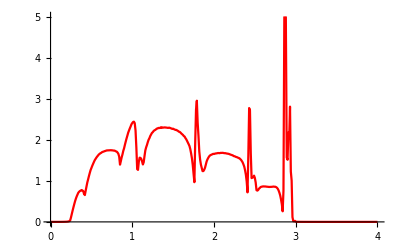

```mathematica
ListPlot[%173,Joined->True,PlotStyle->Red]
```

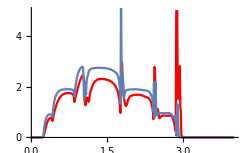

```mathematica
Show[%178,%180]
```

```mathematica
Export["9imp3.csv",%174]
```

9imp3.csv

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.3][[1]],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000974068},{0.01,0.0000717316},{0.02,0.0000516889},{0.03,0.0000442915},{0.04,0.0000398729},{0.05,0.0000468079},{0.06,0.0000573125},{0.07,0.0000812831},{0.08,0.000107818},{0.09,0.000151167},{0.1,0.000201395},{0.11,0.000268078},{0.12,0.000359038},{0.13,0.000472524},{0.14,0.000623293},{0.15,0.000778408},{0.16,0.00103352},{0.17,0.00130626},{0.18,0.0017952},{0.19,0.00235336},{0.2,0.0033254},{0.21,0.00476106},{0.22,0.0073581},{0.23,0.0148118},{0.24,0.106585},{0.25,0.312573},{0.26,0.467328},{0.27,0.583814},{0.28,0.671118},{0.29,0.742376},{0.3,0.791286},{0.31,0.828713},{0.32,0.856724},{0.33,0.876033},{0.34,0.893713},{0.35,0.90262},{0.36,0.909832},{0.37,0.910388},{0.38,0.907757},{0.39,0.900493},{0.4,0.877265},{0.41,0.814452},{0.42,0.839576},{0.43,1.09441},{0.44,1.26391},{0.45,1.38885},{0.46,1.48523},{0.47,1.56178},{0.48,1.62545},{0.49,1.67269},{0.5,1.70806},{0.51,1.74055},{0.52,1.76824},{0.53,1.79193},{0.54,1.81011},{0.55,1.82713},{0.56,1.83759},{0.57,1.85076},{0.58,1.85901},{0.59,1.86673},{0.6,1.87465},{0.61,1.8773},{0.62,1.88129},{0.63,1.8863},{0.64,1.88872},{0.65,1.89042},{0.66,1.89286},{0.67,1.89509},{0.68,1.89555},{0.69,1.89553},{0.7,1.89596},{0.71,1.89583},{0.72,1.89697},{0.73,1.89621},{0.74,1.89549},{0.75,1.8936},{0.76,1.89356},{0.77,1.89089},{0.78,1.88925},{0.79,1.88526},{0.8,1.88091},{0.81,1.8733},{0.82,1.86011},{0.83,1.83803},{0.84,1.78517},{0.85,1.61463},{0.86,1.80852},{0.87,1.98653},{0.88,2.12366},{0.89,2.24509},{0.9,2.34376},{0.91,2.4334},{0.92,2.50167},{0.93,2.56051},{0.94,2.61435},{0.95,2.65313},{0.96,2.69093},{0.97,2.72078},{0.98,2.74122},{0.99,2.76194},{1.,2.77384},{1.01,2.78096},{1.02,2.73575},{1.03,2.35842},{1.04,1.44962},{1.05,2.1665},{1.06,2.17836},{1.07,1.88642},{1.08,1.70183},{1.09,2.15732},{1.1,2.35536},{1.11,2.40483},{1.12,2.47083},{1.13,2.56211},{1.14,2.6217},{1.15,2.65562},{1.16,2.671},{1.17,2.68217},{1.18,2.69743},{1.19,2.70316},{1.2,2.71131},{1.21,2.71507},{1.22,2.71923},{1.23,2.72615},{1.24,2.72363},{1.25,2.72925},{1.26,2.73249},{1.27,2.73503},{1.28,2.73324},{1.29,2.73507},{1.3,2.73727},{1.31,2.7412},{1.32,2.73956},{1.33,2.73696},{1.34,2.73716},{1.35,2.74075},{1.36,2.73566},{1.37,2.73753},{1.38,2.73462},{1.39,2.7327},{1.4,2.73102},{1.41,2.73071},{1.42,2.73029},{1.43,2.72441},{1.44,2.72609},{1.45,2.72212},{1.46,2.72128},{1.47,2.71828},{1.48,2.71562},{1.49,2.70992},{1.5,2.70746},{1.51,2.70423},{1.52,2.70255},{1.53,2.69598},{1.54,2.6922},{1.55,2.68589},{1.56,2.6771},{1.57,2.66757},{1.58,2.65971},{1.59,2.65413},{1.6,2.63823},{1.61,2.62788},{1.62,2.61649},{1.63,2.60598},{1.64,2.59111},{1.65,2.57784},{1.66,2.56308},{1.67,2.54005},{1.68,2.52637},{1.69,2.4971},{1.7,2.45298},{1.71,2.40524},{1.72,2.33869},{1.73,2.23593},{1.74,2.09934},{1.75,1.89176},{1.76,1.33169},{1.77,5.77621},{1.78,2.89586},{1.79,1.73006},{1.8,2.42347},{1.81,2.20847},{1.82,1.68585},{1.83,1.55572},{1.84,1.70197},{1.85,1.77991},{1.86,1.8211},{1.87,1.84332},{1.88,1.85849},{1.89,1.86526},{1.9,1.87084},{1.91,1.87672},{1.92,1.88054},{1.93,1.88165},{1.94,1.88305},{1.95,1.88417},{1.96,1.88671},{1.97,1.8887},{1.98,1.88926},{1.99,1.89146},{2.,1.88889},{2.01,1.89159},{2.02,1.88998},{2.03,1.89134},{2.04,1.89161},{2.05,1.89301},{2.06,1.89157},{2.07,1.89216},{2.08,1.89188},{2.09,1.88834},{2.1,1.88737},{2.11,1.8869},{2.12,1.88546},{2.13,1.88252},{2.14,1.87973},{2.15,1.87564},{2.16,1.87454},{2.17,1.86981},{2.18,1.8667},{2.19,1.86353},{2.2,1.86027},{2.21,1.85569},{2.22,1.85389},{2.23,1.85193},{2.24,1.85073},{2.25,1.84758},{2.26,1.84329},{2.27,1.83999},{2.28,1.83755},{2.29,1.83124},{2.3,1.82258},{2.31,1.81012},{2.32,1.79918},{2.33,1.77719},{2.34,1.75278},{2.35,1.72137},{2.36,1.68545},{2.37,1.63618},{2.38,1.59079},{2.39,1.53038},{2.4,1.41832},{2.41,1.02487},{2.42,2.15766},{2.43,0.789898},{2.44,1.35002},{2.45,2.17751},{2.46,1.47841},{2.47,0.974313},{2.48,0.869895},{2.49,0.910398},{2.5,0.935095},{2.51,0.945486},{2.52,0.9528},{2.53,0.95638},{2.54,0.958075},{2.55,0.957975},{2.56,0.957722},{2.57,0.957339},{2.58,0.955469},{2.59,0.956124},{2.6,0.95481},{2.61,0.953767},{2.62,0.954475},{2.63,0.952444},{2.64,0.953373},{2.65,0.953465},{2.66,0.955554},{2.67,0.955248},{2.68,0.956747},{2.69,0.957439},{2.7,0.957262},{2.71,0.956373},{2.72,0.95441},{2.73,0.948004},{2.74,0.940407},{2.75,0.927946},{2.76,0.910531},{2.77,0.890651},{2.78,0.86911},{2.79,0.842997},{2.8,0.817883},{2.81,0.790806},{2.82,0.766906},{2.83,0.74591},{2.84,0.68153},{2.85,0.863348},{2.86,0.0731255},{2.87,0.201726},{2.88,1.3117},{2.89,1.22832},{2.9,0.449256},{2.91,0.0221701},{2.92,0.00441402},{2.93,0.00295883},{2.94,0.0020356},{2.95,0.00153666},{2.96,0.00120447},{2.97,0.000974719},{2.98,0.000803169},{2.99,0.000666411},{3.,0.000553576},{3.01,0.000468417},{3.02,0.000412131},{3.03,0.000349262},{3.04,0.00030602},{3.05,0.000265227},{3.06,0.000236289},{3.07,0.000208157},{3.08,0.000188049},{3.09,0.00016743},{3.1,0.000142963},{3.11,0.000134304},{3.12,0.00012195},{3.13,0.000107534},{3.14,0.000098637},{3.15,0.0000922939},{3.16,0.000081444},{3.17,0.0000753509},{3.18,0.0000684482},{3.19,0.0000618815},{3.2,0.0000576989},{3.21,0.0000524303},{3.22,0.0000485825},{3.23,0.0000460263},{3.24,0.0000421447},{3.25,0.000037709},{3.26,0.0000355295},{3.27,0.0000328938},{3.28,0.0000307346},{3.29,0.0000281165},{3.3,0.0000258564},{3.31,0.0000254581},{3.32,0.0000232012},{3.33,0.0000221457},{3.34,0.0000202314},{3.35,0.0000192131},{3.36,0.0000180846},{3.37,0.0000167299},{3.38,0.0000152882},{3.39,0.0000146143},{3.4,0.0000137589},{3.41,0.0000132074},{3.42,0.0000122933},{3.43,0.0000114422},{3.44,0.0000107231},{3.45,0.0000101143},{3.46,9.73018×10^-6},{3.47,8.90769×10^-6},{3.48,8.58118×10^-6},{3.49,8.4713×10^-6},{3.5,7.48132×10^-6},{3.51,7.52656×10^-6},{3.52,6.74917×10^-6},{3.53,6.4599×10^-6},{3.54,6.21054×10^-6},{3.55,5.82556×10^-6},{3.56,5.62933×10^-6},{3.57,5.40135×10^-6},{3.58,4.95604×10^-6},{3.59,4.78013×10^-6},{3.6,4.57739×10^-6},{3.61,4.4899×10^-6},{3.62,4.13891×10^-6},{3.63,3.8378×10^-6},{3.64,3.80955×10^-6},{3.65,3.60066×10^-6},{3.66,3.48982×10^-6},{3.67,3.21265×10^-6},{3.68,3.09658×10^-6},{3.69,2.91162×10^-6},{3.7,2.84064×10^-6},{3.71,2.6504×10^-6},{3.72,2.53674×10^-6},{3.73,2.48133×10^-6},{3.74,2.33399×10^-6},{3.75,2.17677×10^-6},{3.76,2.12078×10^-6},{3.77,2.041×10^-6},{3.78,2.00263×10^-6},{3.79,1.88418×10^-6},{3.8,1.77516×10^-6},{3.81,1.67221×10^-6},{3.82,1.60783×10^-6},{3.83,1.59447×10^-6},{3.84,1.53929×10^-6},{3.85,1.45036×10^-6},{3.86,1.3368×10^-6},{3.87,1.36342×10^-6},{3.88,1.30311×10^-6},{3.89,1.24124×10^-6},{3.9,1.16628×10^-6},{3.91,1.13775×10^-6},{3.92,1.09397×10^-6},{3.93,1.07253×10^-6},{3.94,1.02373×10^-6},{3.95,9.79119×10^-7},{3.96,9.32702×10^-7},{3.97,8.90246×10^-7},{3.98,8.39288×10^-7},{3.99,8.30191×10^-7},{4.,8.1262×10^-7}}

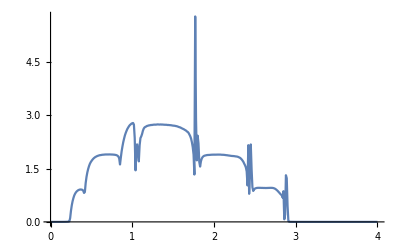

```mathematica
ListPlot[%174,Joined->True]
```

```mathematica
Export["9imp9.csv",%175]
```

9imp9.csv

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.9][[1]],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0202054},{0.01,0.0158864},{0.02,0.0138061},{0.03,0.0107405},{0.04,0.00895245},{0.05,0.0073021},{0.06,0.00640567},{0.07,0.00583706},{0.08,0.00454438},{0.09,0.00427526},{0.1,0.004132},{0.11,0.00378038},{0.12,0.00383714},{0.13,0.00367609},{0.14,0.00389975},{0.15,0.00425782},{0.16,0.00470333},{0.17,0.00539505},{0.18,0.00602396},{0.19,0.00702837},{0.2,0.00908137},{0.21,0.0118239},{0.22,0.0153913},{0.23,0.0224709},{0.24,0.0276444},{0.25,0.0344073},{0.26,0.0526589},{0.27,0.0722554},{0.28,0.0956249},{0.29,0.124694},{0.3,0.16331},{0.31,0.199814},{0.32,0.238429},{0.33,0.278289},{0.34,0.318804},{0.35,0.362089},{0.36,0.400374},{0.37,0.433528},{0.38,0.460275},{0.39,0.478687},{0.4,0.487451},{0.41,0.495558},{0.42,0.502758},{0.43,0.517314},{0.44,0.536913},{0.45,0.567463},{0.46,0.610746},{0.47,0.640379},{0.48,0.677581},{0.49,0.708122},{0.5,0.744835},{0.51,0.782659},{0.52,0.821473},{0.53,0.853222},{0.54,0.893585},{0.55,0.92955},{0.56,0.964616},{0.57,1.0032},{0.58,1.03844},{0.59,1.07486},{0.6,1.09711},{0.61,1.13896},{0.62,1.16758},{0.63,1.18137},{0.64,1.20814},{0.65,1.23142},{0.66,1.25761},{0.67,1.27194},{0.68,1.28589},{0.69,1.30131},{0.7,1.31549},{0.71,1.32767},{0.72,1.33719},{0.73,1.34498},{0.74,1.35041},{0.75,1.34683},{0.76,1.35336},{0.77,1.35217},{0.78,1.35238},{0.79,1.33886},{0.8,1.33297},{0.81,1.31101},{0.82,1.27981},{0.83,1.23233},{0.84,1.14568},{0.85,1.00558},{0.86,1.05114},{0.87,1.08571},{0.88,1.12361},{0.89,1.15518},{0.9,1.19609},{0.91,1.22558},{0.92,1.25777},{0.93,1.29658},{0.94,1.33554},{0.95,1.38282},{0.96,1.4397},{0.97,1.47632},{0.98,1.51645},{0.99,1.55907},{1.,1.60683},{1.01,1.65336},{1.02,1.68933},{1.03,1.72308},{1.04,1.72492},{1.05,1.67631},{1.06,1.5935},{1.07,1.45884},{1.08,1.28768},{1.09,1.12408},{1.1,0.986598},{1.11,0.911133},{1.12,0.859191},{1.13,0.844733},{1.14,0.864984},{1.15,0.878224},{1.16,0.894493},{1.17,0.93117},{1.18,0.946655},{1.19,0.964302},{1.2,0.957208},{1.21,0.943547},{1.22,0.929773},{1.23,0.899043},{1.24,0.907927},{1.25,0.900221},{1.26,0.903998},{1.27,0.937166},{1.28,0.950417},{1.29,0.985393},{1.3,1.01204},{1.31,1.03815},{1.32,1.06422},{1.33,1.08739},{1.34,1.11359},{1.35,1.12952},{1.36,1.15149},{1.37,1.15846},{1.38,1.17923},{1.39,1.19631},{1.4,1.19949},{1.41,1.22046},{1.42,1.22815},{1.43,1.22922},{1.44,1.23993},{1.45,1.25191},{1.46,1.25696},{1.47,1.25023},{1.48,1.25106},{1.49,1.2519},{1.5,1.25288},{1.51,1.251},{1.52,1.24545},{1.53,1.2378},{1.54,1.21763},{1.55,1.22112},{1.56,1.2124},{1.57,1.20404},{1.58,1.17778},{1.59,1.16225},{1.6,1.14214},{1.61,1.11861},{1.62,1.10765},{1.63,1.08019},{1.64,1.04495},{1.65,1.01877},{1.66,0.994814},{1.67,0.955988},{1.68,0.909379},{1.69,0.864122},{1.7,0.808998},{1.71,0.778996},{1.72,0.743848},{1.73,0.687619},{1.74,0.687587},{1.75,0.759934},{1.76,1.09604},{1.77,2.26147},{1.78,2.03867},{1.79,2.02991},{1.8,1.99267},{1.81,1.8949},{1.82,1.71739},{1.83,1.57306},{1.84,1.51627},{1.85,1.31951},{1.86,1.23747},{1.87,1.13592},{1.88,1.08289},{1.89,1.0317},{1.9,1.0216},{1.91,0.973925},{1.92,0.93384},{1.93,0.923298},{1.94,0.818371},{1.95,0.841349},{1.96,0.745765},{1.97,0.725067},{1.98,0.729794},{1.99,0.692588},{2.,0.702524},{2.01,0.698662},{2.02,0.720401},{2.03,0.725482},{2.04,0.747689},{2.05,0.766352},{2.06,0.804245},{2.07,0.819072},{2.08,0.840206},{2.09,0.864981},{2.1,0.885581},{2.11,0.895043},{2.12,0.909097},{2.13,0.919392},{2.14,0.936558},{2.15,0.939548},{2.16,0.959122},{2.17,0.949814},{2.18,0.964519},{2.19,0.966557},{2.2,0.961568},{2.21,0.974448},{2.22,0.972335},{2.23,0.966465},{2.24,0.960371},{2.25,0.952502},{2.26,0.949478},{2.27,0.93439},{2.28,0.9278},{2.29,0.913436},{2.3,0.89681},{2.31,0.881164},{2.32,0.866388},{2.33,0.827546},{2.34,0.80506},{2.35,0.774281},{2.36,0.741248},{2.37,0.702095},{2.38,0.647861},{2.39,0.579843},{2.4,0.52755},{2.41,0.597767},{2.42,1.47246},{2.43,1.46072},{2.44,1.2444},{2.45,1.32721},{2.46,1.20525},{2.47,1.08403},{2.48,1.13644},{2.49,1.20865},{2.5,1.19939},{2.51,1.20976},{2.52,1.17463},{2.53,1.0852},{2.54,1.13796},{2.55,1.01696},{2.56,0.895993},{2.57,1.05678},{2.58,0.941372},{2.59,0.830466},{2.6,0.803024},{2.61,0.725351},{2.62,0.806137},{2.63,0.693892},{2.64,0.628428},{2.65,0.572933},{2.66,0.543429},{2.67,0.530929},{2.68,0.517254},{2.69,0.506492},{2.7,0.502452},{2.71,0.502434},{2.72,0.50144},{2.73,0.494226},{2.74,0.481741},{2.75,0.473899},{2.76,0.454603},{2.77,0.438472},{2.78,0.422646},{2.79,0.399143},{2.8,0.379313},{2.81,0.36324},{2.82,0.342225},{2.83,0.361962},{2.84,0.438179},{2.85,7.95095},{2.86,19.9259},{2.87,18.7179},{2.88,10.9632},{2.89,11.6576},{2.9,6.55556},{2.91,8.36085},{2.92,21.9218},{2.93,10.7603},{2.94,9.33688},{2.95,7.47734},{2.96,11.9202},{2.97,10.3624},{2.98,7.54348},{2.99,7.51701},{3.,3.08047},{3.01,2.67476},{3.02,3.4129},{3.03,2.46327},{3.04,3.871},{3.05,1.42057},{3.06,2.07826},{3.07,0.505382},{3.08,0.739326},{3.09,1.65063},{3.1,0.256464},{3.11,0.291662},{3.12,0.045153},{3.13,0.255432},{3.14,0.986893},{3.15,0.00740202},{3.16,0.00609023},{3.17,0.00295694},{3.18,0.00230899},{3.19,0.00312905},{3.2,0.00173522},{3.21,0.00155564},{3.22,0.00134726},{3.23,0.0012663},{3.24,0.00109309},{3.25,0.00097851},{3.26,0.000892597},{3.27,0.00084023},{3.28,0.000726457},{3.29,0.000681901},{3.3,0.000600094},{3.31,0.000556677},{3.32,0.000522941},{3.33,0.000488745},{3.34,0.000433841},{3.35,0.000404879},{3.36,0.000367111},{3.37,0.000344362},{3.38,0.000327497},{3.39,0.000299114},{3.4,0.000281171},{3.41,0.000264835},{3.42,0.000235029},{3.43,0.000224808},{3.44,0.000207411},{3.45,0.000196914},{3.46,0.000180904},{3.47,0.000170722},{3.48,0.000161727},{3.49,0.000146629},{3.5,0.000141144},{3.51,0.000128399},{3.52,0.000123504},{3.53,0.000118595},{3.54,0.000112941},{3.55,0.000107306},{3.56,0.0000991317},{3.57,0.0000906275},{3.58,0.0000886704},{3.59,0.0000826291},{3.6,0.0000781402},{3.61,0.000072863},{3.62,0.0000687351},{3.63,0.0000649095},{3.64,0.0000626185},{3.65,0.0000579143},{3.66,0.0000550869},{3.67,0.0000527689},{3.68,0.000050506},{3.69,0.0000490085},{3.7,0.0000430957},{3.71,0.0000428993},{3.72,0.0000421966},{3.73,0.0000390033},{3.74,0.0000376805},{3.75,0.0000355663},{3.76,0.0000351192},{3.77,0.0000325612},{3.78,0.0000310706},{3.79,0.0000294945},{3.8,0.0000278594},{3.81,0.0000266832},{3.82,0.00002568},{3.83,0.0000244924},{3.84,0.0000235492},{3.85,0.0000226865},{3.86,0.00002143},{3.87,0.0000199445},{3.88,0.0000197657},{3.89,0.00001867},{3.9,0.0000179857},{3.91,0.0000175168},{3.92,0.0000163454},{3.93,0.000015971},{3.94,0.0000150976},{3.95,0.0000148258},{3.96,0.0000139142},{3.97,0.0000133338},{3.98,0.000012505},{3.99,0.000011929},{4.,0.0000117286}}